#### Extracting all lines from scripts

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}]
```

{L1045,u0,m0,BIANCA,They do not!,L1044,u2,m0,CAMERON,They do to!,L985,1524452,L666257,u9030,m616,DURNFORD,Good ones yes Mr Vereker. Gentlemen who can ride and shoot,L666256,u9034,m616,VEREKER,Colonel Durnford... William Vereker. I hear you 've been seeking Officers?}
 |  |  |  |

```mathematica
lines=StringReplace[Partition[data,5][[All,-1]],{"\""->""}];
```

```mathematica
linesJoined=StringJoin[Riffle[lines," "]]
```

```mathematica
Riffle[lines," "]
```

```mathematica
lines//Length
```

304894

```mathematica
sentences=TextCases[linesJoined,"Sentence"];
```

#### Extracting and modifying questions from lines

Replacing “?” for “.” and making letters of lower case

```mathematica
questions=ToLowerCase[StringReplace[Select[sentences,StringContainsQ[#,"?"]&],{"?"->"."}]]
```

{she okay.,you know how sometimes you just become this persona.,and you don't know how to quit.,like my fear of wearing pastels.,what good stuff.,what crap.,19642,well what's the point of waiting.,it's sixth century b.c.  do you like the period.,dance.,okay.,what are you going to do.}
 |  |  |  |

#### Extracting and modifying normal sentences from lines

```mathematica
normalLines=ToLowerCase[Complement[sentences,questions][[80;;64213]]]
```

{a.,a..,a .45-- colt peacemaker.,aaa!,aaaaaaaaaa!,64125,wade i got a message for you.,wade it's late.,wade sarge corporal insect all of us hell i'll bet even the captain has a mother.,wade's right it's some kind of scientific magnetic thing i can't explain it but i've seen it.}
 |  |  |  |

```mathematica
normalLines1=RandomSample[normalLines,19653]
```

{coppers figured he laundered money for the mob before getting into real estate.,make it fast i'm expecting someone.,here's the deal:,how do you know how bad it was?,19645,hey-ho..,did you come here with wally--to *not* watch movies?,a hospital is no place for secrecy, mr. treves.,no time.}
 |  |  |  |

#### Random Sample

```mathematica
SeedRandom[1234];trainquestions1=RandomSample[questions,13757]
```

{did ya get the license number.,you gonna pull.,we've known debbie what since the eighth grade.,joyce give the assistant chief inspector a drink would you.,13749,miss wollsten shares the room with you.,what do you want to know evan.,will these boards hold.,like my fear of wearing pastels.}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions1=RandomSample[normalLines1,13757]
```

{i sat on his lap and got ahold of him and wiggled and wiggled my ass on him and was worse'n you could know a child like you.,i can't follow you.,how long have you been here?,just to see if i could do it.,13749,she's upset.,are you fuckin' kidding me?,it's alright janet.,how do you know how bad it was?}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq1=RandomSample[Complement[questions,trainquestions1],2000]
```

```mathematica
SeedRandom[1234];validationnonq1=RandomSample[Complement[normalLines1,trainnonquestions1],2000]
```

```mathematica
SeedRandom[1234];testq1=RandomSample[Complement[questions,trainquestions1,validationq1],2600]
```

```mathematica
SeedRandom[1234];testnonq1=RandomSample[Complement[normalLines1,trainnonquestions1,validationnonq1],2600]
```

```mathematica
StringJoin[Riffle[TextStructure["like my fear of wearing pastels.","PartsOfSpeech"][[1,1,1,All,2,1,2]]," "]]
```

$Aborted

#### Changing parts of speech to numbers

```mathematica
(TextStructure[,"PartsOfSpeech"][[1,1,1,All,2,1,2]])
```

```mathematica
Union[{"Preposition","Pronoun","Noun","Preposition","Verb","Noun","Punctuation"}]
```

```mathematica
{"Noun","Preposition","Pronoun","Punctuation","Verb"}//Length
```

5

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
{"Preposition","Pronoun","Noun","Preposition","Verb","Noun","Punctuation"}/. rules
```

{2,3,1,2,5,1,4}

#### Classify

```mathematica
Classify[<|"Not a question"->{{"like my fear of wearing pastels.",{"Preposition","Pronoun","Noun","Preposition","Verb","Noun","Punctuation"}},{"like your fear of wearing pastels.",{"Preposition","Pronoun","Noun","Preposition","Verb","Noun","Punctuation"}}},"Question"->{{"like my fer of wearing pastels.",{"Preposition","Pronoun","Noun","Preposition","Verb","Noun","Punctuation"}},{"like your fear of pearing pastels.",{"Preposition","Pronoun","Noun","Preposition","Verb","Noun","Punctuation"}}}|>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
categories = Union[Flatten[Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;1000]]]]]
```

{Adjective,Adverb,Conjunction,Determiner,Interjection,Missing,Noun,Numeral,Particle,Preposition,Pronoun,ProperNoun,Punctuation,Symbol,Verb}

```mathematica
partsOfSpeechNumbers [ x_] := Transpose[
{ x,
Map[
(
 (
  (
   (
     TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]]
    )/.Missing[]->{"","Missing"}
   )
  )
  [[All,2]]
) 
& , x ]
/. rules}] ;
```

```mathematica
Transpose[{questions[[1;;10]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;10]]]/.rules}]
```

{{she okay.,{11,1,13}},{you know how sometimes you just become this persona.,{11,15,2,2,11,2,15,4,7,13}},{and you don't know how to quit.,{3,11,15,2,15,2,10,15,13}},{like my fear of wearing pastels.,{10,11,7,10,15,7,13}},{what good stuff.,{4,1,7,13}},{what crap.,{4,7,13}},{do you listen to this crap.,{15,11,15,10,4,7,13}},{you always been this selfish.,{11,2,15,4,1,13}},{you never wanted to go out with 'me did you.,{11,2,15,10,15,9,10,13,11,15,11,13}},{i was.,{6,15,13}}}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;1000]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;1000]]]}], "Not Question"->Transpose[{normalLines1[[1;;1000]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;1000]]]}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;100]]]}], "Not Question"->Transpose[{validationnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;100]]]}] |>]
```

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]}] |>]
```

ClassifierMeasurementsObject[…]

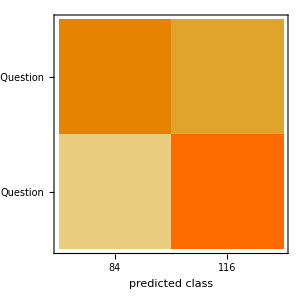

```mathematica
cm["ConfusionMatrixPlot"]
```

### With Vector Numbers

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]/.rules}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]/.rules}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]/.rules}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]/.rules}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]/.rules}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]/.rules}] |>]
```

ClassifierMeasurementsObject[…]

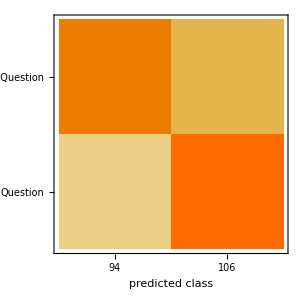

```mathematica
cm["ConfusionMatrixPlot"]
```

### Classify with 1000 sentences per class

```mathematica
partsOfSpeechNumbers [ questions[[1;;100]] ]
```

```mathematica
cl1000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;2000]]],

"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;2000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;200]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;200]]] |>,

PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cl1000
```

```mathematica
cm =ClassifierMeasurements[cl1000,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;500]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

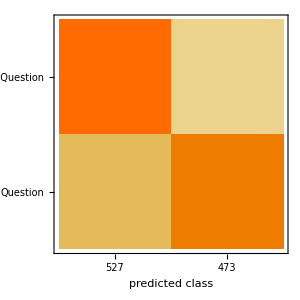

```mathematica
cm["ConfusionMatrixPlot"]
```

### 5000

```mathematica
cl5000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;5000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;500]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;500]]] |>,

PerformanceGoal->"Speed"]
```